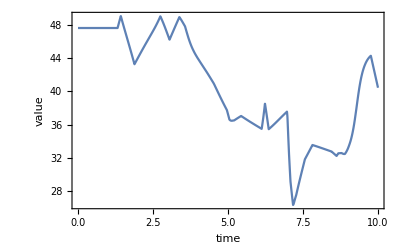

```mathematica
plotHamValues
```

```mathematica
Chop[MF[Ts[[6]]]]
```

(Cos[$q3[t]] | -Sin[$q3[t]] | 0 | 1. $q1[t]
Sin[$q3[t]] | Cos[$q3[t]] | 0 | 1. $q2[t]
0 | 0 | 1. | 0
0 | 0 | 0 | 1.)

```mathematica
MF[Ts[[11]]]
```

(-0.0475651 | 0.998868 | 0 | 2.1
-0.998868 | -0.0475651 | 0 | -0.1
0 | 0 | 1. | 0
0 | 0 | 0 | 1.)

```mathematica
plotHamValues:=Module[{},
Show[Plot[
Evaluate[Piecewise[{ham}/.data]],{t,0,2},PlotLegends->"Hamilton",
	PlotRange->Automatic,Frame->True,FrameLabel->{"time","value"}
]]]
plotHamValues
```

Piecewise::pairs: The first argument {{3.97078+9.97877 Cos[{«1»,«23»,{InterpolatingFunction[«5»][«1»],«9»[«3»]}}[t]]+«25»+0.3 ({{«2»},«23»,{«2»}}'[t])^2}} of Piecewise is not a list of pairs.

InterpolatingFunction::dmval: Input value {0.0000408571} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

Piecewise::pairs: The first argument {{3.97078+9.97877 Cos[{«1»}[0.0000408571]]+«24»+«1»+0.3 ({{«2»},«23»,{«2»}}'[0.0000408571])^2}} of Piecewise is not a list of pairs.

General::stop: Further output of Piecewise::pairs will be suppressed during this calculation.

-Graphics-